```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[8],Join[Table[{i,i-1},{i,Range[2,8,1]}],Table[{i,i+1},{i,Range[1,8,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[8]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,1,0]],A:=Inverse[β[ω,δ,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[8]-A.T.J.T].A,60000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SL[ω,δ,1,0].T[1].SR[ω,δ,1,0].T[1]].SL[ω,δ,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SR[ω,δ,1,0].T[1].SL[ω,δ,1,0].T[1]].SR[ω,δ,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.99996},{0.01,7.99996},{0.02,7.99998},{0.03,7.99998},{0.04,7.99998},{0.05,7.99997},{0.06,7.99996},{0.07,7.99997},{0.08,7.99999},{0.09,7.99996},{0.1,7.99996},{0.11,7.99994},{0.12,7.9935},{0.13,7.},{0.14,6.99999},{0.15,6.99999},{0.16,6.99998},{0.17,6.99998},{0.18,6.99997},{0.19,6.99998},{0.2,6.99997},{0.21,6.99998},{0.22,6.99996},{0.23,6.99999},{0.24,6.99998},{0.25,6.99997},{0.26,6.99997},{0.27,6.99998},{0.28,6.99999},{0.29,6.99998},{0.3,6.99999},{0.31,6.99998},{0.32,6.99998},{0.33,6.99997},{0.34,6.99998},{0.35,6.99998},{0.36,6.99999},{0.37,6.99997},{0.38,6.99997},{0.39,6.99998},{0.4,6.99997},{0.41,6.99996},{0.42,6.99996},{0.43,6.99997},{0.44,6.99997},{0.45,6.99997},{0.46,6.99994},{0.47,6.00053},{0.48,5.99999},{0.49,5.99998},{0.5,5.99998},{0.51,5.99995},{0.52,5.99998},{0.53,5.99999},{0.54,5.99997},{0.55,5.99996},{0.56,5.99996},{0.57,5.99999},{0.58,5.99997},{0.59,5.99997},{0.6,5.99999},{0.61,5.99996},{0.62,5.99997},{0.63,5.99998},{0.64,5.99999},{0.65,5.99998},{0.66,5.99997},{0.67,5.99999},{0.68,5.99996},{0.69,5.99996},{0.7,5.99998},{0.71,5.99997},{0.72,5.99999},{0.73,5.99998},{0.74,5.99997},{0.75,5.99998},{0.76,5.99997},{0.77,5.99998},{0.78,5.99999},{0.79,5.99997},{0.8,5.99996},{0.81,5.99997},{0.82,5.99999},{0.83,5.99997},{0.84,5.99997},{0.85,5.99999},{0.86,5.99996},{0.87,5.99999},{0.88,5.99999},{0.89,5.99996},{0.9,5.99998},{0.91,5.99998},{0.92,5.99998},{0.93,5.99997},{0.94,5.99996},{0.95,5.99995},{0.96,5.99997},{0.97,5.99995},{0.98,5.99996},{0.99,5.99993},{1.,5.49995},{1.01,4.99998},{1.02,4.99996},{1.03,4.99996},{1.04,4.99995},{1.05,4.99995},{1.06,4.99997},{1.07,4.99996},{1.08,4.99997},{1.09,4.99998},{1.1,4.99997},{1.11,4.99996},{1.12,4.99998},{1.13,4.99998},{1.14,4.99997},{1.15,4.99998},{1.16,4.99997},{1.17,4.99995},{1.18,4.99997},{1.19,4.99997},{1.2,4.99997},{1.21,4.99999},{1.22,4.99997},{1.23,4.99997},{1.24,4.99995},{1.25,4.99998},{1.26,4.99995},{1.27,4.99996},{1.28,5.},{1.29,4.99998},{1.3,4.99998},{1.31,4.99999},{1.32,4.99998},{1.33,4.99998},{1.34,4.99998},{1.35,4.99998},{1.36,4.99996},{1.37,4.99997},{1.38,4.99996},{1.39,4.99995},{1.4,4.99997},{1.41,4.99998},{1.42,4.99994},{1.43,4.99997},{1.44,4.99996},{1.45,4.99997},{1.46,4.99995},{1.47,4.99997},{1.48,4.99996},{1.49,4.99995},{1.5,4.99995},{1.51,4.99996},{1.52,4.99996},{1.53,4.99996},{1.54,4.99997},{1.55,4.99995},{1.56,4.99997},{1.57,4.99995},{1.58,4.99996},{1.59,4.99997},{1.6,4.99998},{1.61,4.99998},{1.62,4.99996},{1.63,4.99997},{1.64,4.99994},{1.65,4.99963},{1.66,4.00004},{1.67,3.99998},{1.68,3.99999},{1.69,3.99997},{1.7,3.99997},{1.71,3.99997},{1.72,3.99999},{1.73,3.99996},{1.74,3.99997},{1.75,3.99997},{1.76,3.99999},{1.77,3.99998},{1.78,3.99996},{1.79,3.99998},{1.8,3.99999},{1.81,3.99998},{1.82,3.99997},{1.83,3.99997},{1.84,3.99998},{1.85,3.99997},{1.86,3.99997},{1.87,3.99996},{1.88,3.99997},{1.89,3.99997},{1.9,3.99997},{1.91,3.99998},{1.92,3.99996},{1.93,3.99996},{1.94,3.99996},{1.95,3.99996},{1.96,3.99998},{1.97,3.99998},{1.98,3.99998},{1.99,3.99997},{2.,3.99997},{2.01,3.99998},{2.02,3.99997},{2.03,3.99998},{2.04,3.99996},{2.05,3.99998},{2.06,3.99999},{2.07,3.99997},{2.08,3.99997},{2.09,3.99996},{2.1,3.99997},{2.11,4.},{2.12,3.99997},{2.13,3.99997},{2.14,3.99998},{2.15,3.99999},{2.16,3.99998},{2.17,3.99999},{2.18,3.99999},{2.19,3.99998},{2.2,3.99998},{2.21,3.99999},{2.22,4.},{2.23,3.99999},{2.24,3.99999},{2.25,3.99999},{2.26,3.99998},{2.27,3.99998},{2.28,4.},{2.29,3.99999},{2.3,3.99998},{2.31,3.99999},{2.32,3.99997},{2.33,3.99997},{2.34,3.99994},{2.35,3.00034},{2.36,3.},{2.37,2.99998},{2.38,2.99999},{2.39,2.99999},{2.4,2.99999},{2.41,2.99999},{2.42,3.},{2.43,2.99998},{2.44,2.99999},{2.45,2.99998},{2.46,3.},{2.47,2.99998},{2.48,2.99999},{2.49,2.99999},{2.5,2.99999},{2.51,3.},{2.52,2.99999},{2.53,3.},{2.54,2.99999},{2.55,2.99999},{2.56,2.99999},{2.57,3.},{2.58,2.99999},{2.59,3.},{2.6,2.99999},{2.61,2.99999},{2.62,3.},{2.63,2.99999},{2.64,3.},{2.65,2.99999},{2.66,3.},{2.67,2.99999},{2.68,2.99999},{2.69,2.99999},{2.7,2.99999},{2.71,2.99999},{2.72,2.99999},{2.73,3.},{2.74,2.99999},{2.75,2.99999},{2.76,3.},{2.77,3.},{2.78,2.99999},{2.79,3.},{2.8,2.99999},{2.81,3.},{2.82,3.},{2.83,3.},{2.84,3.},{2.85,3.},{2.86,3.},{2.87,3.},{2.88,3.},{2.89,3.},{2.9,3.},{2.91,3.},{2.92,3.},{2.93,3.},{2.94,3.},{2.95,3.},{2.96,3.},{2.97,3.},{2.98,2.99999},{2.99,2.99997},{3.,2.49999},{3.01,2.00002},{3.02,2.},{3.03,2.},{3.04,2.},{3.05,2.},{3.06,2.},{3.07,2.},{3.08,2.},{3.09,2.},{3.1,2.},{3.11,2.},{3.12,2.},{3.13,2.},{3.14,2.},{3.15,2.},{3.16,2.},{3.17,2.},{3.18,2.},{3.19,2.},{3.2,2.},{3.21,2.},{3.22,2.},{3.23,2.},{3.24,2.},{3.25,2.},{3.26,2.},{3.27,2.},{3.28,2.},{3.29,2.},{3.3,2.},{3.31,2.},{3.32,2.},{3.33,2.},{3.34,2.},{3.35,2.},{3.36,2.},{3.37,2.},{3.38,2.},{3.39,2.},{3.4,2.},{3.41,2.},{3.42,2.},{3.43,2.},{3.44,2.},{3.45,2.},{3.46,2.},{3.47,2.},{3.48,2.},{3.49,2.},{3.5,2.},{3.51,1.99999},{3.52,1.99998},{3.53,1.99943},{3.54,1.00004},{3.55,1.00001},{3.56,1.},{3.57,1.},{3.58,1.},{3.59,1.},{3.6,1.},{3.61,1.},{3.62,1.},{3.63,1.},{3.64,1.},{3.65,1.},{3.66,1.},{3.67,1.},{3.68,1.},{3.69,1.},{3.7,1.},{3.71,1.},{3.72,1.},{3.73,1.},{3.74,1.},{3.75,1.},{3.76,1.},{3.77,1.},{3.78,1.},{3.79,1.},{3.8,1.},{3.81,0.999999},{3.82,0.999999},{3.83,0.999999},{3.84,0.999998},{3.85,0.999997},{3.86,0.999993},{3.87,0.999972},{3.88,0.00648459},{3.89,0.0000220888},{3.9,5.84101×10^-6},{3.91,2.64451×10^-6},{3.92,1.50192×10^-6},{3.93,9.67492×10^-7},{3.94,6.75391×10^-7},{3.95,4.98544×10^-7},{3.96,3.8342×10^-7},{3.97,3.04303×10^-7},{3.98,2.47592×10^-7},{3.99,2.05551×10^-7},{4.,1.73514×10^-7}}

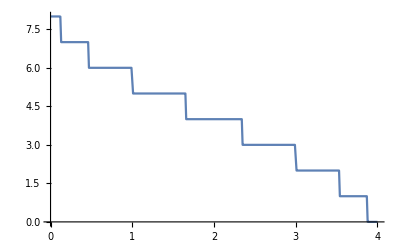

```mathematica
ListPlot[pris,Joined->True]
```

```mathematica
μ1=RandomInteger[{1,8}]; μ2=RandomInteger[{1,8}]; μ3=RandomInteger[{1,8}]; μ4=RandomInteger[{1,8}];μ5=RandomInteger[{1,8}]; μ6=RandomInteger[{1,8}]; μ7=RandomInteger[{1,8}];μ8=RandomInteger[{1,8}](*; μ9=RandomInteger[{1,8}]; μ10=RandomInteger[{1,8}]; μ11=RandomInteger[{1,8}];μ12=RandomInteger[{1,8}]; μ13=RandomInteger[{1,8}]; μ14=RandomInteger[{1,8}]*)
```

6

```mathematica
deltae[ω_,ϵ1_,n_]:=Module[{Tin=T[1],μ1=RandomInteger[{1,8}], μ2=RandomInteger[{1,8}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,8}],μ5=RandomInteger[{1,8}], μ6=RandomInteger[{1,8}], μ7=RandomInteger[{1,8}],μ8=RandomInteger[{1,8}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
(*imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
*)imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-0]]];
list={{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[8]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]];,{ζ,1,n}];
 J=J]];
b]
```

```mathematica
RandomSample[{imp,imp,imp,imp1,imp3,imp5,imp14,imp,imp,imp,imp2,imp,imp5,imp,imp4,imp,imp12,imp1,imp,imp,imp8,imp,imp,imp8,imp3,imp,imp,imp,imp,imp,imp4,imp,imp11,imp3,imp,imp,imp,imp,imp,imp13,imp7,imp,imp4,imp7,imp9,imp,imp2,imp14,imp5,imp,imp,imp,imp,imp13,imp6,imp,imp,imp10,imp11,imp,imp12,imp,imp,imp14,imp,imp,imp,imp11,imp,imp,imp,imp6,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp6,imp,imp13,imp9,imp10,imp2,imp10,imp7,imp,imp12,imp,imp8,imp,imp,imp,imp9}]
```

{imp,imp,imp,imp,imp,imp13,imp13,imp,imp7,imp,imp,imp,imp,imp3,imp1,imp2,imp7,imp,imp,imp,imp,imp,imp,imp9,imp13,imp12,imp,imp,imp11,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp6,imp,imp10,imp14,imp,imp,imp,imp5,imp,imp,imp,imp,imp2,imp,imp,imp3,imp,imp1,imp3,imp6,imp8,imp14,imp,imp1,imp,imp11,imp10,imp,imp,imp,imp10,imp,imp4,imp12,imp,imp9,imp,imp,imp,imp4,imp9,imp,imp11,imp,imp,imp12,imp2,imp,imp,imp,imp4,imp7,imp14,imp5,imp,imp,imp,imp6,imp5,imp,imp8}

```mathematica
ir[ω_,ϵ1_]:= Inverse[IdentityMatrix[8]-SR[ω,0.0001,1,0].T[1].deltae[ω,ϵ1,8].T[1]].SR[ω,0.0001,1,0]
```

```mathematica
GN[ω_,ϵ1_]:=deltae[ω,ϵ1,1].T[1].deltae[ω,ϵ1,2].T[1].deltae[ω,ϵ1,3].T[1].deltae[ω,ϵ1,4].T[1].deltae[ω,ϵ1,5].T[1].deltae[ω,ϵ1,6].T[1].deltae[ω,ϵ1,7].T[1].deltae[ω,ϵ1,8].T[1].ir[ω,ϵ1]
```

```mathematica
Ε[ω_]:= T[1].SL[ω,0.0001,1,0].T[1]
```

```mathematica
Γ[ω_]:= ⅈ(Ε[ω]-ConjugateTranspose[Ε[ω]])
```

```mathematica
TRA[ω_,ϵ1_]:=Abs[Tr[Γ[ω].GN[ω,ϵ1].Γ[ω].ConjugateTranspose[GN[ω,ϵ1]]]]
```

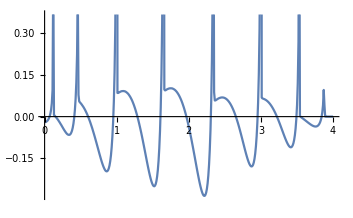

```mathematica
ListLinePlot[Table[{ω,-Im[GN[ω,0][[1,1]]]},{ω,Range[0,4,0.01]}]]
```

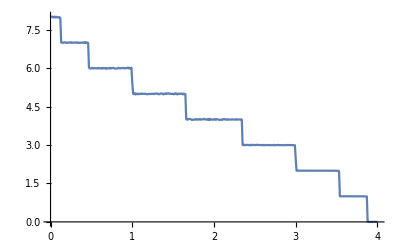

```mathematica
ListLinePlot[Table[{ω,TRA[ω,0]},{ω,Range[0,4,0.01]}]]
```